```mathematica
Clear[l1,l2,l2,a1,a2,a3,b1,b2,b3,c1,c2,c3,a,b,c,t1,t2,dot,cross]
```

```mathematica
l1={a1,b1,c1}
l2={a2,b2,c2}
```

{a1,b1,c1}

{a2,b2,c2}

```mathematica
l3={a3,b3,c3}
```

{a3,b3,c3}

```mathematica
w={l1,l2}
dot={l1.l2==-1}
cross=Cross[l1,l2]
```

{{a1,b1,c1},{a2,b2,c2}}

{a1 a2+b1 b2+c1 c2==-1}

{-b2 c1+b1 c2,a2 c1-a1 c2,-a2 b1+a1 b2}

```mathematica
t1=Table[l3[[i]]==cross[[i]],{i,3}]
```

{a3==-b2 c1+b1 c2,b3==a2 c1-a1 c2,c3==-a2 b1+a1 b2}

```mathematica
{Norm[cross]==0}
```

{√(Abs[-a2 b1+a1 b2]^2+Abs[a2 c1-a1 c2]^2+Abs[-b2 c1+b1 c2]^2)==0}

```mathematica
nc={(-a2 b1+a1 b2)^2+(a2 c1-a1 c2)^2+(-b2 c1+b1 c2)^2==3}
```

{(-a2 b1+a1 b2)^2+(a2 c1-a1 c2)^2+(-b2 c1+b1 c2)^2==3}

```mathematica
a={{b1,c1},{b2,c2}}
```

{{b1,c1},{b2,c2}}

```mathematica
b={{c1,a1},{c2,a1}}
```

{{c1,a1},{c2,a1}}

```mathematica
c={{a1,b1},{a2,b2}}
```

{{a1,b1},{a2,b2}}

```mathematica
wt=Transpose[w]
```

{{a1,a2},{b1,b2},{c1,c2}}

```mathematica
ww=w.wt
```

{{a1^2+b1^2+c1^2,a1 a2+b1 b2+c1 c2},{a1 a2+b1 b2+c1 c2,a2^2+b2^2+c2^2}}

```mathematica
A2={{2,-1},{0,-1}}
```

{{2,-1},{0,-1}}

```mathematica
Flatten[Table[ww[[i,j]]==A2[[i,j]],{i,2},{j,2}]]
```

{a1^2+b1^2+c1^2==2,a1 a2+b1 b2+c1 c2==-1,a1 a2+b1 b2+c1 c2==0,a2^2+b2^2+c2^2==-1}

```mathematica
Clear[t2]
```

```mathematica
t2={a1^2+b1^2+c1^2==2,a1 a2+b1 b2+c1 c2==-1,a1 a2+b1 b2+c1 c2==-1,a2^2+b2^2+c2^2==2}
```

{a1^2+b1^2+c1^2==2,a1 a2+b1 b2+c1 c2==-1,a1 a2+b1 b2+c1 c2==-1,a2^2+b2^2+c2^2==2}

```mathematica
(* A_2 in C^3 as SL(2,c) three perpendicular lines solved*)
```

```mathematica
v=Join[dot,t1,t2,nc,{Det[a]==1},{Det[b]==1},{Det[c]==1}]
```

{a1 a2+b1 b2+c1 c2==-1,a3==-b2 c1+b1 c2,b3==a2 c1-a1 c2,c3==-a2 b1+a1 b2,a1^2+b1^2+c1^2==2,a1 a2+b1 b2+c1 c2==-1,a1 a2+b1 b2+c1 c2==-1,a2^2+b2^2+c2^2==2,(-a2 b1+a1 b2)^2+(a2 c1-a1 c2)^2+(-b2 c1+b1 c2)^2==3,-b2 c1+b1 c2==1,a1 c1-a1 c2==1,-a2 b1+a1 b2==1}

```mathematica
Length[v]
```

12

```mathematica
(* the eight solutions are equivalent to SU(3) matrices unnormalized*)
```

```mathematica
sv={l1,l2,l3}/.NSolve[v,{a1,b1,c1,a2,b2,c2,a3,b3,c3}]
```

{{{-0.57735,1.1547,-0.57735},{-0.57735,-0.57735,1.1547},{1.,1.,1.}},{{-1.,1.,0.},{0.,-1.,1.},{1.,1.,1.}},{{-0.349297-0.67479 ⅈ,-1.30359-0.180809 ⅈ,-0.954297+0.493981 ⅈ},{1.30359+0.180809 ⅈ,0.954297-0.493981 ⅈ,-0.349297-0.67479 ⅈ},{1.,-1.,1.}},{{-0.349297+0.67479 ⅈ,-1.30359+0.180809 ⅈ,-0.954297-0.493981 ⅈ},{1.30359-0.180809 ⅈ,0.954297+0.493981 ⅈ,-0.349297+0.67479 ⅈ},{1.,-1.,1.}},{{0.349297-0.67479 ⅈ,1.30359-0.180809 ⅈ,0.954297+0.493981 ⅈ},{-1.30359+0.180809 ⅈ,-0.954297-0.493981 ⅈ,0.349297-0.67479 ⅈ},{1.,-1.,1.}},{{0.349297+0.67479 ⅈ,1.30359+0.180809 ⅈ,0.954297-0.493981 ⅈ},{-1.30359-0.180809 ⅈ,-0.954297+0.493981 ⅈ,0.349297+0.67479 ⅈ},{1.,-1.,1.}},{{0.57735,-1.1547,0.57735},{0.57735,0.57735,-1.1547},{1.,1.,1.}},{{1.,-1.,0.},{0.,1.,-1.},{1.,1.,1.}}}

```mathematica
(*showing the 8 solutions are orthogonal*)
```

```mathematica
{l1,l2,l3}.Inverse[{l1,l2,l3}]/.NSolve[v,{a1,b1,c1,a2,b2,c2,a3,b3,c3}]//Chop
```

{{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}},{{1.,0,0},{0,1.,0},{0,0,1.}}}

```mathematica
Dimensions[sv]
```

{8,3,3}

```mathematica
Table[Det[sv[[i]]]//Chop,{i,Length[sv]}]
```

{3.,3.,3.,3.,3.,3.,3.,3.}

```mathematica
sv12={l1,l2}.Transpose[{l1,l2}]/.NSolve[v,{a1,b1,c1,a2,b2,c2,a3,b3,c3}]//Chop
```

{{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}},{{2.,-1.},{-1.,2.}}}

```mathematica
(*5 unique Killing vectors*)
```

```mathematica
kl=Union[Rationalize[Table[sv[[i]].{1,1,1},{i,Length[sv]}]//Chop]]
```

{{-2.60719-0.361619 ⅈ,1.90859-0.987961 ⅈ,1},{-2.60719+0.361619 ⅈ,1.90859+0.987961 ⅈ,1},{0,0,3},{2.60719-0.361619 ⅈ,-1.90859-0.987961 ⅈ,1},{2.60719+0.361619 ⅈ,-1.90859+0.987961 ⅈ,1}}

```mathematica
pj=Table[(kl[[i,1]]+I*kl[[i,2]])/(1+kl[[i,3]]),{i,Length[kl]}]
```

{-0.809614+0.773488 ⅈ,-1.79758+1.13511 ⅈ,0,1.79758-1.13511 ⅈ,0.809614-0.773488 ⅈ}

```mathematica
Fit[pj,{1,x},x]
```

(-2.05008+1.60925 ⅈ)+(0.683361-0.536417 ⅈ) x

```mathematica
(*Complex Plane stereographic projection*)
```

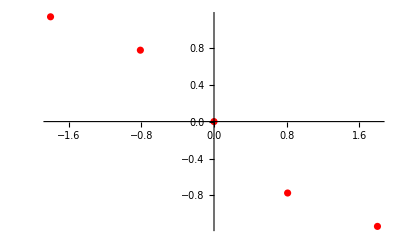

```mathematica
ComplexListPlot[pj,ImageSize->Full,PlotStyle->Red]
```

```mathematica
Length[kl]
```

5

```mathematica
Eigenvalues[kl.Transpose[kl]]//Chop
```

{41.4507,13.,-4.11734,0,0}

```mathematica
Transpose[kl].kl//Chop
```

{{26.6667,-21.3333,0},{-21.3333,10.6667,0},{0,0,13.}}

```mathematica
ca48=Table[2*kl[[i]].kl[[j]]/(kl[[i]].kl[[i]]),{i,5},{j,5}]//Chop
```

{{2.,2.35019+0.428862 ⅈ,0.561934+0.102541 ⅈ,-1.97557-0.360501 ⅈ,-1.62538+0.0683608 ⅈ},{2.35019-0.428862 ⅈ,2.,0.561934-0.102541 ⅈ,-1.62538-0.0683608 ⅈ,-1.97557+0.360501 ⅈ},{0.666667,0.666667,2,0.666667,0.666667},{-1.97557+0.360501 ⅈ,-1.62538-0.0683608 ⅈ,0.561934-0.102541 ⅈ,2.,2.35019-0.428862 ⅈ},{-1.62538+0.0683608 ⅈ,-1.97557-0.360501 ⅈ,0.561934+0.102541 ⅈ,2.35019+0.428862 ⅈ,2.}}

```mathematica
TableForm[ca48]
```

2. | 2.35019+0.428862 ⅈ | 0.561934+0.102541 ⅈ | -1.97557-0.360501 ⅈ | -1.62538+0.0683608 ⅈ
2.35019-0.428862 ⅈ | 2. | 0.561934-0.102541 ⅈ | -1.62538-0.0683608 ⅈ | -1.97557+0.360501 ⅈ
0.666667 | 0.666667 | 2 | 0.666667 | 0.666667
-1.97557+0.360501 ⅈ | -1.62538-0.0683608 ⅈ | 0.561934-0.102541 ⅈ | 2. | 2.35019-0.428862 ⅈ
-1.62538+0.0683608 ⅈ | -1.97557-0.360501 ⅈ | 0.561934+0.102541 ⅈ | 2.35019+0.428862 ⅈ | 2.

```mathematica
Eigenvalues[ca48]//Chop
```

{8.02204,2.74924,-0.771289,0,0}

```mathematica
WeightedAdjacencyGraph[ca48]
```

-Graphics-

```mathematica
(*end*)
```